# 36: Lanczos Iteration

Arnoldi and all sorts of other stuff gets simpler for symmetric matrices. As you would expect Upper Hessenberg matrices become tridiagonal.  One other thing that happens is the general Arnoldi Iteration gets called Lanczos in the special symmetric case. Just as a reminder the Krylov space is 	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b})
and Arnoldi iteratively computes a nested sequence of orthonormal basis for the Krylov space (represented by orthogonal matrices Q_n∈ℝ^(m×n)) and a rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n) which represents the action of A on these basis through
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
The question is what simplifies when A is real symmetric.  We are going to look at the Arnoldi code and work out what can be tidied up.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Not surprisingly the Hessenberg matrix becomes symmetric tridiagonal.

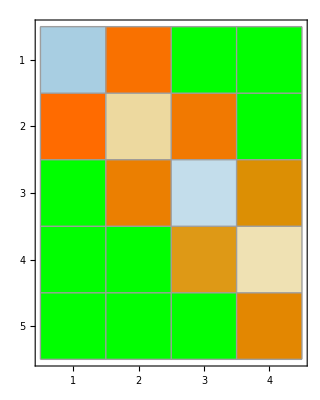

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
b=Normalize[RandomReal[{-1,1},m]];
{Q0,H0}={{b}ᵀ,{{}}};
{Q1,H1}=Arnoldi[A][{Q0,H0}];
{Q2,H2}=Arnoldi[A][{Q1,H1}];
{Q3,H3}=Arnoldi[A][{Q2,H2}];
{Q4,H4}=Arnoldi[A][{Q3,H3}];
MatrixPlot[Chop[H4],ColorRules->{0->Green},Mesh->All]
```

A glance at the code explains this simplification. By construction A.q_j∈Span(q_1,q_2,.…,q_j,q_(j+1)) and q_i.q_j=0 for i≠j with (again by construction) H_(i,j)=q_j.A.q_i . This means H_(i,j)=q_i.A.q_j=0 for i>j+1. If A is real symmetric i.e A=Aᵀ then 
	  H_(i,j)=q_i.A.q_j=q_j.Aᵀ.q_j=q_j.A.q_j=H_(j,i).
So elements of H more than one off the diagonal are zero while the sub and super diagonals match.  The Lanczos iteration incorporates this simplification and stores the diagonal entries α_n and off-diagonal entries β_n in vectors.

```mathematica
Lanczos[A_][{Q_,{α_,β_}}]:= Module[{m,n,w,βNew,αNew,qNew},
{m,n}=Dimensions[Q];
w=A.Q⟦All,n⟧;
βNew=w.Q⟦All,n⟧;
w=w-βNew Q⟦All,n⟧;
αNew=Norm[w];
qNew=w/αNew;
{ArrayFlatten[({{Q, {qNew}ᵀ}})],{Append[α,αNew],Append[β,βNew]}}
]
```

Testing

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
q0=Normalize[RandomReal[{-1,1},m]];
q1=A.q0;
β1=q0.q1;
q1=q1-β1 q0;
α1=Norm[q1];
q2=
```

```mathematica
{α,β}={
{Q0,{α0,β0}}={{b}ᵀ,{{},{}}};
n=2;
{Q,{α,β}}=Nest[Lanczos[A],{Q0,{α0,β0}},n]
```

{{{-0.333468,0.0730199,-0.554298},{0.0154239,0.218714,-0.135541},{0.348447,0.109734,0.331834},{-0.164535,-0.557135,-0.170243},{-0.419633,-0.0469401,-0.342911},{0.238344,-0.491056,0.294111},{0.404459,-0.226714,0.227788},{0.273555,0.0145502,-0.396426},{0.00793076,0.355991,0.066156},{0.270065,-0.175104,0.151234},{0.18165,0.396999,0.288624},{-0.403435,-0.120172,-0.107717}},{{2.51323,3.8003},{0.190051,-0.340255}}}

```mathematica
Map[Norm,Qᵀ]
```

{1.,1.,1.}

```mathematica
Qᵀ.Q
```

{{1.,-4.16334×10^-17,0.661323},{-4.16334×10^-17,1.,-2.08167×10^-17},{0.661323,-2.08167×10^-17,1.}}

SparseArray[…]

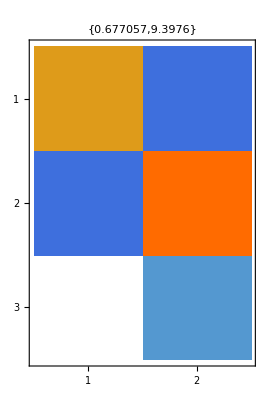

```mathematica
H=SparseArray[{Band[{1,1}]->α,Band[{1,2}]->Drop[β,-1],Band[{2,1}]->β}]
MatrixPlot[H,
PlotLabel->{Norm[Qᵀ.Q-IdentityMatrix[n+1]],Norm[A.Q⟦All,n⟧-Q.H]}]
```

```mathematica
Map[Dimensions,{Q,H}]
Q⟦All,⟧.H
```

{{12,7},{7,7}}

Dot::dotsh: Tensors {{-0.125585,0.0751056,-0.0411402,0.31329,-0.0877635,0.384106},«9»,«2»} and SparseArray[Automatic,«1»,0,{1,{{0,2,5,8,11,14,17,19},{«1»}},{-0.907616,1,-0.907616,2.78684,1.89,0.562654,3.71257,1.89,0.562654,2.10661,«9»}}] have incompatible shapes.

{{-0.125585,0.0751056,-0.0411402,0.31329,-0.0877635,0.384106},{-0.0457186,-0.223045,-0.277448,-0.291278,-0.216741,-0.222449},{0.406848,0.245201,0.341492,0.139068,0.214256,0.145307},{-0.166497,0.43064,-0.212687,0.290767,-0.282275,0.204719},{0.314013,0.0472399,-0.195448,-0.223844,-0.192219,-0.226473},{-0.245927,-0.0831083,-0.23511,-0.18457,-0.202325,-0.222247},{-0.387208,0.439168,-0.432868,0.245378,-0.482496,0.175097},{-0.264079,-0.173445,-0.289951,-0.128905,-0.312671,-0.150864},{0.283546,0.383674,0.146598,0.192378,0.188506,0.186378},{0.194834,-0.55443,0.0473639,-0.708003,-0.0520376,-0.714465},{-0.373265,-0.0876778,-0.0845693,0.0583823,0.0577826,0.0685129},{0.390454,0.0682658,0.60305,-0.102162,0.608035,-0.189637}}.SparseArray[…]

```mathematica
?Append
```